```mathematica
Clear[B,Bx,Bz,nz,nx,n,k,kx,kz,ϕ,ϕmm,R00,R11,R01,Rpp,Rmm,Rpm];
```

```mathematica
B=Sqrt[Bx^2+Bz^2];
nx=Bx/B;
nz=Bz/B;
R00=Cos[B]-I*nz*Sin[B];
R11=Cos[B]+I*nz*Sin[B];
R01=-I*nx*Sin[B];
Rpp=Cos[B]-I*nx*Sin[B];
Rmm=Cos[B]+I*nx*Sin[B];
Rpm=-I*nz*Sin[B];
```

```mathematica
R11abs=Sqrt[Cos[B]^2+(nz*Sin[B])^2];
ϕ=ArcTan[nz*Tan[B]];
RnkZ=R11abs^(n-kx)*Exp[-I*ϕ*(n-kx)]*Exp[-I*kx*Pi/2]*(nx*Sin[B])^kx+R11abs^kx*Exp[I*ϕ*kx]*Exp[-I*(n-kx)*Pi/2]*(nx*Sin[B])^(n-kx);
RnkZconj=R11abs^(n-kx)*Exp[I*ϕ*(n-kx)]*Exp[I*kx*Pi/2]*(nx*Sin[B])^kx+R11abs^kx*Exp[-I*ϕ*kx]*Exp[I*(n-kx)*Pi/2]*(nx*Sin[B])^(n-kx);
```

```mathematica
Rmmabs=Sqrt[Cos[B]^2+(nx*Sin[B])^2];
ϕmm=ArcTan[nx*Tan[B]];
RnkX=Rmmabs^(n-kz)*Exp[-I*ϕmm*(n-kz)]*Exp[-I*kz*Pi/2]*(nz*Sin[B])^kz+Rmmabs^kz*Exp[I*ϕmm*kz]*Exp[-I*(n-kz)*Pi/2]*(nz*Sin[B])^(n-kz);
RnkXconj=Rmmabs^(n-kz)*Exp[I*ϕmm*(n-kz)]*Exp[I*kz*Pi/2]*(nz*Sin[B])^kz+Rmmabs^kz*Exp[-I*ϕmm*kz]*Exp[I*(n-kz)*Pi/2]*(nz*Sin[B])^(n-kz);
```

```mathematica
folderPath="/home/mauricio/Documents/Research/QEC/QSensing/QECn1CFI/";
FoutcomesXX=Import[FileNameJoin[{folderPath,"FoutcomesXX.mx"}]];
FoutcomesZZ=Import[FileNameJoin[{folderPath,"FoutcomesZZ.mx"}]];
FoutcomesXZ=Import[FileNameJoin[{folderPath,"FoutcomesXZ.mx"}]];
FBeffXX=Import[FileNameJoin[{folderPath,"FBeffXX.mx"}]];
FBeffZZ=Import[FileNameJoin[{folderPath,"FBeffZZ.mx"}]];
FBeffXZ=Import[FileNameJoin[{folderPath,"FBeffXZ.mx"}]];
FoutcomeskzXX=Import[FileNameJoin[{folderPath,"FoutcomeskzXX.mx"}]];
FoutcomeskzZZ=Import[FileNameJoin[{folderPath,"FoutcomeskzZZ.mx"}]];
FoutcomeskzXZ=Import[FileNameJoin[{folderPath,"FoutcomeskzXZ.mx"}]];
FBeffkzXX=Import[FileNameJoin[{folderPath,"FBeffkzXX.mx"}]];
FBeffkzZZ=Import[FileNameJoin[{folderPath,"FBeffkzZZ.mx"}]];
FBeffkzXZ=Import[FileNameJoin[{folderPath,"FBeffkzXZ.mx"}]];
```

```mathematica
CFIZxx=FoutcomesXX+FBeffXX;
CFIZzz=FoutcomesZZ+FBeffZZ;
CFIZxz=FoutcomesXZ+FBeffXZ;
CFIZmat={{CFIZxx,CFIZxz},{CFIZxz,CFIZzz}};
```

```mathematica
CFIXxx=FoutcomeskzXX+FBeffkzXX;
CFIXzz=FoutcomeskzZZ+FBeffkzZZ;
CFIXxz=FoutcomeskzXZ+FBeffkzXZ;
CFIXmat={{CFIXxx,CFIXxz},{CFIXxz,CFIXzz}};
```

```mathematica
CFImat=CFIZmat+CFIXmat;
```

## Probe in the Z basis

```mathematica
Bxaux=0.1;
Bzaux=1.;
nmin=7;
nmax=29;
QFIZTraceList={};
CFIZTraceList1={};
CFIZTraceList2={};

For[naux=nmin,naux<=nmax,naux+=4,

QFIZmat1xx=Sum[Binomial[n,kx]*D[RnkZconj,Bx]*D[RnkZ,Bx]/.n->naux,{kx,0,naux}];
QFIZmat1zz=Sum[Binomial[n,kx]*D[RnkZconj,Bz]*D[RnkZ,Bz]/.n->naux,{kx,0,naux}];
QFIZmat1xz=Sum[Binomial[n,kx]*D[RnkZconj,Bx]*D[RnkZ,Bz]/.n->naux,{kx,0,naux}];
QFIZmat1zx=Sum[Binomial[n,kx]*D[RnkZconj,Bz]*D[RnkZ,Bx]/.n->naux,{kx,0,naux}];
QFIZmat1={{QFIZmat1xx,QFIZmat1xz},{QFIZmat1zx,QFIZmat1zz}};

QFIZmat2xx=Sum[Binomial[n,kx]*RnkZconj*D[RnkZ,Bx]/.n->naux,{kx,0,naux}]*Sum[Binomial[n,kx]*RnkZ*D[RnkZconj,Bx]/.n->naux,{kx,0,naux}];
QFIZmat2zz=Sum[Binomial[n,kx]*RnkZconj*D[RnkZ,Bz]/.n->naux,{kx,0,naux}]*Sum[Binomial[n,kx]*RnkZ*D[RnkZconj,Bz]/.n->naux,{kx,0,naux}];
QFIZmat2xz=Sum[Binomial[n,kx]*RnkZconj*D[RnkZ,Bz]/.n->naux,{kx,0,naux}]*Sum[Binomial[n,kx]*RnkZ*D[RnkZconj,Bx]/.n->naux,{kx,0,naux}];
QFIZmat2zx=Sum[Binomial[n,kx]*RnkZconj*D[RnkZ,Bx]/.n->naux,{kx,0,naux}]*Sum[Binomial[n,kx]*RnkZ*D[RnkZconj,Bz]/.n->naux,{kx,0,naux}];
QFIZmat2={{QFIZmat2xx,QFIZmat2xz},{QFIZmat2zx,QFIZmat2zz}};


QFIZmat=(2*QFIZmat1-QFIZmat2)/.{Bx->Bxaux,Bz->Bzaux};
AppendTo[QFIZTraceList,{naux,Re[Tr[Inverse[QFIZmat]]]}];

AppendTo[CFIZTraceList1,{naux,Tr[Inverse[CFIZmat/.{Bx->Bxaux,Bz->Bzaux,n->naux}]]}];
AppendTo[CFIZTraceList2,{naux,Tr[Inverse[CFIZmat/.{Bx->Bxaux,Bz->Bzaux,n->(naux-1)/2}]]}];

];
```

## Probe in the X basis

```mathematica
Bxaux=0.1;
Bzaux=1.;
nmin=7;
nmax=29;
QFIXTraceList={};
CFIXTraceList1={};
CFIXTraceList2={};

For[naux=nmin,naux<=nmax,naux+=4,

QFIXmat1xx=Sum[Binomial[n,kz]*D[RnkXconj,Bx]*D[RnkX,Bx]/.n->naux,{kz,0,naux}];
QFIXmat1zz=Sum[Binomial[n,kz]*D[RnkXconj,Bz]*D[RnkX,Bz]/.n->naux,{kz,0,naux}];
QFIXmat1xz=Sum[Binomial[n,kz]*D[RnkXconj,Bx]*D[RnkX,Bz]/.n->naux,{kz,0,naux}];
QFIXmat1zx=Sum[Binomial[n,kz]*D[RnkXconj,Bz]*D[RnkX,Bx]/.n->naux,{kz,0,naux}];
QFIXmat1={{QFIXmat1xx,QFIXmat1xz},{QFIXmat1zx,QFIXmat1zz}};

QFIXmat2xx=Sum[Binomial[n,kz]*RnkXconj*D[RnkX,Bx]/.n->naux,{kz,0,naux}]*Sum[Binomial[n,kz]*RnkX*D[RnkXconj,Bx]/.n->naux,{kz,0,naux}];
QFIXmat2zz=Sum[Binomial[n,kz]*RnkXconj*D[RnkX,Bz]/.n->naux,{kz,0,naux}]*Sum[Binomial[n,kz]*RnkX*D[RnkXconj,Bz]/.n->naux,{kz,0,naux}];
QFIXmat2xz=Sum[Binomial[n,kz]*RnkXconj*D[RnkX,Bz]/.n->naux,{kz,0,naux}]*Sum[Binomial[n,kz]*RnkX*D[RnkXconj,Bx]/.n->naux,{kz,0,naux}];
QFIXmat2zx=Sum[Binomial[n,kz]*RnkXconj*D[RnkX,Bx]/.n->naux,{kz,0,naux}]*Sum[Binomial[n,kz]*RnkX*D[RnkXconj,Bz]/.n->naux,{kz,0,naux}];
QFIXmat2={{QFIXmat2xx,QFIXmat2xz},{QFIXmat2zx,QFIXmat2zz}};


QFIXmat=(2*QFIXmat1-QFIXmat2)/.{Bx->Bxaux,Bz->Bzaux};
AppendTo[QFIXTraceList,{naux,Re[Tr[Inverse[QFIXmat]]]}];

AppendTo[CFIXTraceList1,{naux,Tr[Inverse[CFIXmat/.{Bx->Bxaux,Bz->Bzaux,n->naux}]]}];
AppendTo[CFIXTraceList2,{naux,Tr[Inverse[CFIXmat/.{Bx->Bxaux,Bz->Bzaux,n->(naux-1)/2}]]}];


];
```

```mathematica
QFIZTraceList
CFIZTraceList1
CFIZTraceList2
QFIXTraceList
CFIXTraceList1
CFIXTraceList2
```

{{7,0.0557161},{11,0.0342672},{15,0.0247224},{19,0.0193316},{23,0.0158693},{27,0.0134582}}

{{7,0.0557161},{11,0.0342672},{15,0.0247224},{19,0.0193316},{23,0.0158693},{27,0.0134582}}

{{7,0.145955},{11,0.0808764},{15,0.0557161},{19,0.0424472},{23,0.0342672},{27,0.0287245}}

{{7,0.0543301},{11,0.0311316},{15,0.0214665},{19,0.0162733},{23,0.0130619},{27,0.0108903}}

{{7,0.0543301},{11,0.0311316},{15,0.0214665},{19,0.0162733},{23,0.0130619},{27,0.0108903}}

{{7,0.158102},{11,0.0829199},{15,0.0543301},{19,0.0397841},{23,0.0311316},{27,0.0254534}}

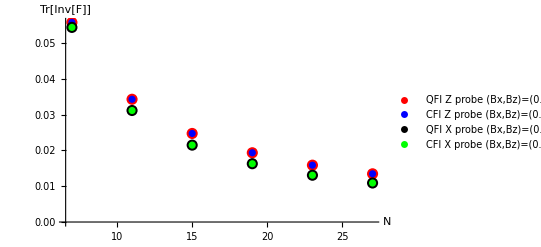

```mathematica
Show[
ListPlot[QFIZTraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI Z probe (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListPlot[CFIZTraceList1,PlotStyle->{Blue,Thick},PlotLegends->{"CFI Z probe (Bx,Bz)=(0.1,1)"}],
ListPlot[QFIXTraceList,PlotStyle->{Black,PointSize[0.02]},PlotLegends->{"QFI X probe (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListPlot[CFIXTraceList1,PlotStyle->{Green,Thick},PlotLegends->{"CFI X probe (Bx,Bz)=(0.1,1)"}]
]
```

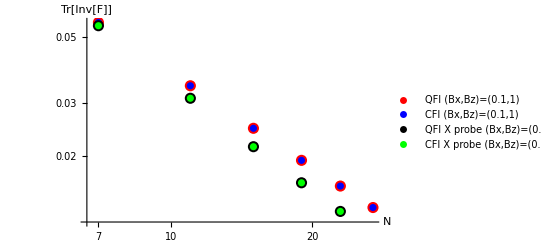

```mathematica
Show[
ListLogLogPlot[QFIZTraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFIZTraceList1,PlotStyle->{Blue,Thick},PlotLegends->{"CFI (Bx,Bz)=(0.1,1)"}],
ListLogLogPlot[QFIXTraceList,PlotStyle->{Black,PointSize[0.02]},PlotLegends->{"QFI X probe (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFIXTraceList1,PlotStyle->{Green,Thick},PlotLegends->{"CFI X probe (Bx,Bz)=(0.1,1)"}]
]
```

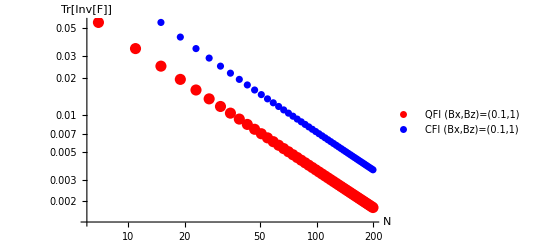

```mathematica
Show[
ListLogLogPlot[QFIZTraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFIZTraceList2,PlotStyle->{Blue,Thick},PlotLegends->{"CFI (Bx,Bz)=(0.1,1)"}]
]
```

## Two probes

```mathematica
Bxaux=0.1;
Bzaux=1.;
nmin=7;
nmax=29;
QFITraceList={};
CFITraceList1={};
CFITraceList2={};

For[naux=nmin,naux<=nmax,naux+=4,

QFImat1xx=Sum[Sum[Binomial[n,kx]*Binomial[n,kz]*D[RnkXconj*RnkZconj,Bx]*D[RnkX*RnkZ,Bx]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat1zz=Sum[Sum[Binomial[n,kx]*Binomial[n,kz]*D[RnkXconj*RnkZconj,Bz]*D[RnkX*RnkZ,Bz]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat1xz=Sum[Sum[Binomial[n,kx]*Binomial[n,kz]*D[RnkXconj*RnkZconj,Bx]*D[RnkX*RnkZ,Bz]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat1zx=Sum[Sum[Binomial[n,kx]*Binomial[n,kz]*D[RnkXconj*RnkZconj,Bz]*D[RnkX*RnkZ,Bx]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat1={{QFImat1xx,QFImat1xz},{QFImat1zx,QFImat1zz}};

QFImat2ax=Sum[Sum[RnkXconj*RnkZconj*D[RnkX*RnkZ,Bx]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat2bx=Sum[Sum[RnkX*RnkZ*D[RnkXconj*RnkZconj,Bx]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat2az=Sum[Sum[RnkXconj*RnkZconj*D[RnkX*RnkZ,Bz]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat2bz=Sum[Sum[RnkX*RnkZ*D[RnkXconj*RnkZconj,Bz]/.n->naux,{kz,0,naux}],{kx,0,naux}];
QFImat2={{QFImat2ax*QFImat2bx,QFImat2az*QFImat2bx},{QFImat2ax*QFImat2bz,QFImat2az*QFImat2az}};

QFImat=(QFImat1-0.25*QFImat2)/.{Bx->Bxaux,Bz->Bzaux};
AppendTo[QFITraceList,{naux,Re[Tr[Inverse[QFImat]]]}];

AppendTo[CFITraceList1,{naux,Tr[Inverse[CFImat/.{Bx->Bxaux,Bz->Bzaux,n->naux}]]}];
AppendTo[CFITraceList2,{naux,Tr[Inverse[CFImat/.{Bx->Bxaux,Bz->Bzaux,n->(naux-1)/2}]]}];


];
```

```mathematica
QFITraceList
CFITraceList1
```

{{7,0.0180812},{11,0.00850396},{15,0.00496334},{19,0.00325775},{23,0.00230394},{27,0.00171614}}

{{7,0.0180556},{11,0.00850296},{15,0.0049633},{19,0.00325774},{23,0.00230394},{27,0.00171614}}

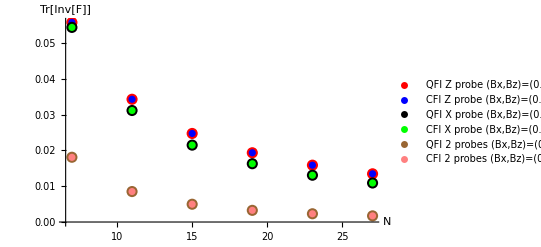

```mathematica
Show[
ListPlot[QFIZTraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI Z probe (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListPlot[CFIZTraceList1,PlotStyle->{Blue,Thick},PlotLegends->{"CFI Z probe (Bx,Bz)=(0.1,1)"}],
ListPlot[QFIXTraceList,PlotStyle->{Black,PointSize[0.02]},PlotLegends->{"QFI X probe (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListPlot[CFIXTraceList1,PlotStyle->{Green,Thick},PlotLegends->{"CFI X probe (Bx,Bz)=(0.1,1)"}],
ListPlot[QFITraceList,PlotStyle->{Brown,PointSize[0.02]},PlotLegends->{"QFI 2 probes (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListPlot[CFITraceList1,PlotStyle->{Pink,Thick},PlotLegends->{"CFI 2 probes (Bx,Bz)=(0.1,1)"}]
]
```

```mathematica
Bxaux=1.;
Bzaux=1.;
nmin=7;
nmax=199;
QFITraceListB={};
CFITraceListB1={};
CFITraceListB2={};

For[naux=nmin,naux<=nmax,naux+=4,

QFIxx=2*Sum[Binomial[n,k]*D[Rnkconj,Bx]*D[Rnk,Bx]/.n->naux,{k,0,naux}]-(Sum[Binomial[n,k]*Rnkconj*D[Rnk,Bx]/.n->naux,{k,0,naux}]*Sum[Binomial[n,k]*Rnk*D[Rnkconj,Bx]/.n->naux,{k,0,naux}]); 
QFIzz=2*Sum[Binomial[n,k]*D[Rnkconj,Bz]*D[Rnk,Bz]/.n->naux,{k,0,naux}]-(Sum[Binomial[n,k]*Rnkconj*D[Rnk,Bz]/.n->naux,{k,0,naux}]*Sum[Binomial[n,k]*Rnk*D[Rnkconj,Bz]/.n->naux,{k,0,naux}]);
QFIxz=2*Sum[Binomial[n,k]*D[Rnkconj,Bx]*D[Rnk,Bz]/.n->naux,{k,0,naux}]-(Sum[Binomial[n,k]*Rnkconj*D[Rnk,Bz]/.n->naux,{k,0,naux}]*Sum[Binomial[n,k]*Rnk*D[Rnkconj,Bx]/.n->naux,{k,0,naux}]);
QFIzx=2*Sum[Binomial[n,k]*D[Rnkconj,Bz]*D[Rnk,Bx]/.n->naux,{k,0,naux}]-(Sum[Binomial[n,k]*Rnkconj*D[Rnk,Bx]/.n->naux,{k,0,naux}]*Sum[Binomial[n,k]*Rnk*D[Rnkconj,Bz]/.n->naux,{k,0,naux}]);
QFImat={{QFIxx,QFIxz},{QFIzx,QFIzz}}/.{Bx->Bxaux,Bz->Bzaux};
AppendTo[QFITraceListB,{naux,Re[Tr[Inverse[QFImat]]]}];

AppendTo[CFITraceListB1,{naux,Tr[Inverse[CFImat/.{Bx->Bxaux,Bz->Bzaux,n->naux}]]}];
AppendTo[CFITraceListB2,{naux,Tr[Inverse[CFImat/.{Bx->Bxaux,Bz->Bzaux,n->(naux-1)/2}]]}];

];
```

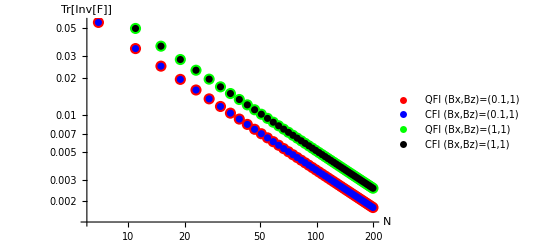

```mathematica
Show[
ListLogLogPlot[QFITraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFITraceList1,PlotStyle->{Blue,Thick},PlotLegends->{"CFI (Bx,Bz)=(0.1,1)"}],
ListLogLogPlot[QFITraceListB,PlotStyle->{Green,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFITraceListB1,PlotStyle->{Black,Thick},PlotLegends->{"CFI (Bx,Bz)=(1,1)"}]
]
```

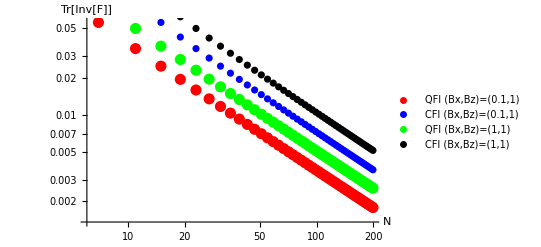

```mathematica
Show[
ListLogLogPlot[QFITraceList,PlotStyle->{Red,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(0.1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFITraceList2,PlotStyle->{Blue,Thick},PlotLegends->{"CFI (Bx,Bz)=(0.1,1)"}],
ListLogLogPlot[QFITraceListB,PlotStyle->{Green,PointSize[0.02]},PlotLegends->{"QFI (Bx,Bz)=(1,1)"},AxesLabel->{"N","Tr[Inv[F]]"}],
ListLogLogPlot[CFITraceListB2,PlotStyle->{Black,Thick},PlotLegends->{"CFI (Bx,Bz)=(1,1)"}]
]
```